```mathematica
∫√(1+(x/p)^2)ⅆx
```

1/2 (x √(1+x^2/p^2)+p ArcSinh[x/p])

```mathematica
∫_(-√(2p a))^(√(2p a)) √(1+(x/p)^2)ⅆx
```

If[Im[p/(√(a p))]≥√2||√2+Im[p/(√(a p))]≤0||Re[p/(√(a p))]≠0,2 √(1/2+a/p) √(a p)+p ArcSinh[(√2 a)/(√(a p))],Integrate[√(1+x^2/p^2),{x,-√2 √(a p),√2 √(a p)},Assumptions→!(Im[p/(√(a p))]≥√2||√2+Im[p/(√(a p))]≤0||Re[p/(√(a p))]≠0)]]

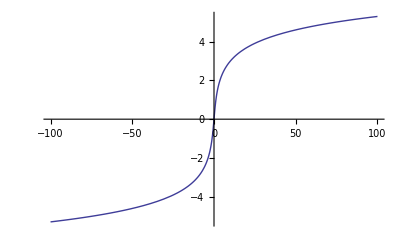

```mathematica
Plot[ArcSinh[x],{x,-100,100}]
```

```mathematica
z=1
Simplify[((ⅇ^z+ⅇ^(-z))/2)-Cosh[z]]
```

1

0

```mathematica
D[ArcSinh[x],x]
```

1/(√(1+x^2))

```mathematica
∫√(1+x^2)ⅆx
```

1/2 (x √(1+x^2)+ArcSinh[x])

```mathematica
D[ArcCosh[x], x]
```

1/(√(-1+x) √(1+x))

```mathematica
∫x^2/(√(x^2+1))ⅆx
```

1/2 x √(1+x^2)-ArcSinh[x]/2

```mathematica
∫√(x^2-1)ⅆx
```

1/2 x √(-1+x^2)-1/2 Log[2 (x+√(-1+x^2))]

```mathematica
D[(x √(x^2-1)-ArcCosh[x]), x]
```

```mathematica
Simplify[Factor[-1/(√(-1+x) √(1+x))+x^2/(√(-1+x^2))+√(-1+x^2)]]
```

-1/(√(-1+x) √(1+x))-1/(√(-1+x^2))+(2 x^2)/(√(-1+x^2))

```mathematica
∫√(1+4/9 x^(-2/3))ⅆx-∫■ⅆ□
```

1/27 √(9+4/x^(2/3)) (4 x^(1/3)+9 x)

```mathematica
∫√(1+x)ⅆx
```

2/3 (1+x)^(3/2)

```mathematica
∫√(1+4/9  x^(-2/3))ⅆx
```

1/27 √(9+4/x^(2/3)) (4 x^(1/3)+9 x)

```mathematica
∫x √(1+4/9 x^2)ⅆx
```

3/4 (1+(4 x^2)/9)^(3/2)

```mathematica
∫_1^a √(1+1/x^2)ⅆx
```

If[(a∉Reals||Re[a]>1||0<Re[a]<1)&&(a/(1-a)∉Reals||Re[a/(1-a)]≤-1||Re[a/(1-a)]≥0),-√2-Log[-1/2+1/(√2)]+(√(1+1/a^2) a (√(1+a^2)+Log[a/2]-Log[1+√(1+a^2)]))/(√(1+a^2)),Integrate[√(1+1/x^2),{x,1,a},Assumptions→!((a∉Reals||Re[a]>1||0<Re[a]<1)&&(a/(1-a)∉Reals||Re[a/(1-a)]≤-1||Re[a/(1-a)]≥0))]]

```mathematica
Simplify[∫√(1+1/x^2)ⅆx]
```

(√(1+1/x^2) x (√(1+x^2)+Log[x]-Log[2 (1+√(1+x^2))]))/(√(1+x^2))

```mathematica
D[((√(1+x^2))+(Log[x/(2+2Sqrt[x^2+1])])), x]
```

x/(√(1+x^2))+((2+2 √(1+x^2)) (-(2 x^2)/(√(1+x^2) (2+2 √(1+x^2))^2)+1/(2+2 √(1+x^2))))/x

```mathematica
x/(√(1+x^2))+((1+√(1+x^2)) (-x^2/(√(1+x^2) (1+√(1+x^2))^2)+1/(1+√(1+x^2))))/x
```

```mathematica
∫√(1+1/x^2)ⅆx
```

(√(1+1/x^2) x (√(1+x^2)+Log[x]-Log[2 (1+√(1+x^2))]))/(√(1+x^2))

```mathematica
D[(ArcSin[x]-(√(x^2+1))/x), x]
```

1/(√(1-x^2))-1/(√(1+x^2))+(√(1+x^2))/x^2

```mathematica
Simplify[D[((√(1+x^2)+Log[x]-Log[2 (1+√(1+x^2))])/1), x]]
```

(1+x^2+√(1+x^2))/(x+x √(1+x^2))

```mathematica
Simplify[D[(√(1+x^2)+Log[√(1+x^2)-1]-Log[1/(√(1+x^2)+1)]), x]]
```

2/x+x/(√(1+x^2))